# (A | 1 | -1 -1 | B | 0 1 | -1 | -1)

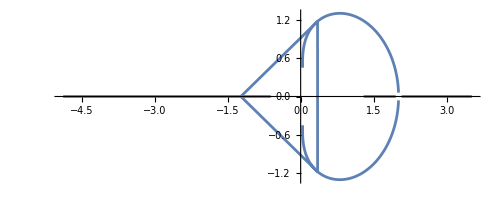

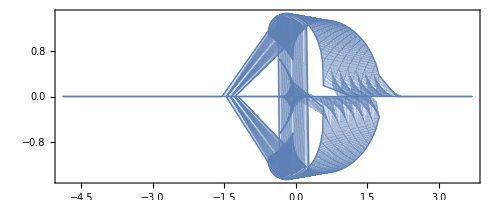

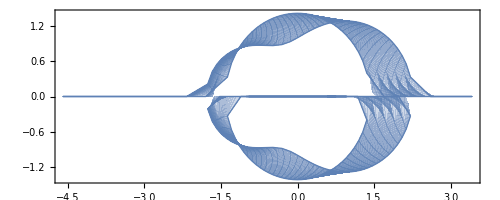

```mathematica
f[a_,b_]:= ReIm[Eigenvalues[{{a,1.0,-1.0},{-1.0,b,0.0},{1.0,-1.0,-1.0}}]]
ParametricPlot[f[1.2,b],{b,-5,4}]
ParametricPlot[f[a,b],{a,0,1},{b,-5,4}]
ParametricPlot[f[a,b],{a,-5,4},{b,0,1}]
```

```mathematica
Clear[a,b]
Collect[CharacteristicPolynomial[{{a,1,-1},{-1,b,0},{1,-1,-1}},λ],λ]
```

-2+b-a b+(-2+a+b-a b) λ+(-1+a+b) λ^2-λ^3

```mathematica
ParametricPlot3D[f[a,b],{a,0, 1},{b,0,2}]
```

-Graphics3D-

```mathematica
Simplify[a/.Solve[ CharacteristicPolynomial[{{a,1,-1},{-1,b,0},{1,-1,-1}},λ]==0,a][[1]]]
Simplify[b/.Solve[ CharacteristicPolynomial[{{a,1,-1},{-1,b,0},{1,-1,-1}},λ]==0,b][[1]]]
```

```mathematica
fa[b_,λ_]=-(2+2 λ+λ^2+λ^3-b (1+λ+λ^2))/((b-λ) (1+λ))
```

-(2+2 λ+λ^2+λ^3-b (1+λ+λ^2))/((b-λ) (1+λ))

```mathematica
fb[a_,λ_]=((1+λ) (2-a λ+λ^2))/(1+λ+λ^2-a (1+λ))
```

((1+λ) (2-a λ+λ^2))/(1+λ+λ^2-a (1+λ))

```mathematica
Manipulate[
ParametricPlot[ReIm[fb[a,x+I y]],{x,1,2},{y,-1,1},
Mesh->All],
{{a,1.4},-4,5,0.1}]
```

P